```mathematica
Run first to set checkboxes ! ! !;
Print[Style["----------------------------------------------------------",Blue]];
Print[Checkbox[Dynamic[drop]],"Drop first image?"]
Print[Checkbox[Dynamic[docalib]],"Do calibration?"]
Print[Checkbox[Dynamic[showSigmas]],"Show sigmas?"]
Print[Checkbox[Dynamic[showNatoms]],"Show N atoms?"]
Print[Checkbox[Dynamic[showCenters]],"Show centers?"]
Print[Checkbox[Dynamic[showPlots]],"Show plots?(Significantly reduces file size!!!)"]
Print[Checkbox[Dynamic[showFitParametes]],"Show fit parameters?"]
Clear[a,b,t,to,τ];
Print["Which fit?\n",RadioButtonBar[Dynamic[whichModel],{1->Style[ToString[a + b Exp[(t-t0)/τ],InputForm],10],2->Style[ToString[a+b Γ/((t-t0)^2+Γ^2),InputForm],10]}]];
Print["Image size\n",RadioButtonBar[Dynamic[imageSize],{1->"big",2->"small"}]];
Print[Style["----------------------------------------------------------",Blue]];
SetDirectory[NotebookDirectory[]]
folders =FileNames["*ms"];
folders = Sort[folders,Internal`StringToDouble[#1]<Internal`StringToDouble[#2]&];
Print["data folders:",folders];
time = Table[Internal`StringToDouble[folders[[i]]],{i,Length[folders]}];
```

----------------------------------------------------------

Drop first image?

Do calibration?

Show sigmas?

Show N atoms?

Show centers?

Show plots?(Significantly reduces file size!!!)

Show fit parameters?

Which fit?
 | a + b*E^((t - t0)/τ)   | a + (b*Γ)/((t - t0)^2 + Γ^2)

Image size
 | big   | small

----------------------------------------------------------

/Volumes/!Data/2015_05_12/test

data folders:{0ms,1ms}

Finding center of cloud

```mathematica
marker="_";
suffics=".png";
filterN = 3;
Clear@imdat;
fc=FileNames[folders[[1]]<>"/*"<>suffics];
(*If[fc=={},fc=FileNames[folders[[1]]<>"/*"<>suffics]];*)
i=3;
imdat= ImageData[Import[fc[[i]]]];
tfcCoord=Flatten[Position[#,Max[#],2,1]&/@{imdat},2];
{widthX,widthY}=Dimensions[imdat];
Print["image size = ",{widthX,widthY}];
Print["Cloud center at ", tfcCoord]
(*tfcCoord={widthX/2,widthY/2};*)
```

image size = {140,112}

Cloud center at {67,46}

```mathematica
Image processing;
```

```mathematica
allInf={};
Print[Dynamic[n]," from ",Length[folders]];
For[n=1,n≤Length[folders],n++,
Clear[files];
cal={};
note={};
files=FileNames[folders[[n]]<>"/*"<>suffics];
If[Length[files]==0,Break[]];

If[drop,files = Drop[files,-1]];

For[i=1,i≤Length[files],i++,
Clear[im];
im =ImageData[Import[files[[i]]]];
AppendTo[allInf,
{Internal`StringToDouble[StringSplit[files[[i]],{"/","_"}][[1]]],Internal`StringToDouble[StringSplit[files[[i]],{"/","_"}][[2]]],
Internal`StringToDouble[StringSplit[files[[i]],{"/","_"}][[3]]],
im,
Abs[Max[im]]
}]
];
]
Print["allInf dimensions: ",Dimensions[allInf]];

Finding pik's amplitudes and background level;
dl=10; (*size of adging *)
dm0 = Dimensions[allInf[[1,4]]];
dm1=Dimensions[allInf[[1,4]][[dl+1;;dm0[[1]]-dl,dl+1;;dm0[[2]]-dl]]];
background=Total[(Total[allInf[[#,4]],2]-Total[allInf[[#,4]][[dl+1;;dm0[[1]]-dl,dl+1;;dm0[[2]]-dl]],2])&/@Range[Length[allInf]]
]/(dm0[[1]]*dm0[[2]]-dm1[[1]]*dm1[[2]])/Length[allInf];
Print["background level: ",background];
noiseLevel=Total[(Total[Abs[allInf[[#,4]]],2]-Total[Abs[allInf[[#,4]]][[dl+1;;dm0[[1]]-dl,dl+1;;dm0[[2]]-dl]],2])&/@Range[Length[allInf]]
]/(dm0[[1]]*dm0[[2]]-dm1[[1]]*dm1[[2]])/Length[allInf];
Print["noise level: ",noiseLevel];
```

from 2

allInf dimensions: {60,5}

background level: 0.000677725

noise level: 0.000677725

```mathematica
Fitting averaged image gata;
```

```mathematica
time = DeleteDuplicates[allInf[[;;,1]]];
i=1;
avrInf={};
modInf={};
Print[Dynamic[n]," from ",Length[time]];
For[n=1,n≤Length[time],n++,
list= Select[allInf,#[[1]]==time[[n]]&];
shotTipes = Sort[DeleteDuplicates[list[[;;,3]]]];
For[i=1,i≤Length[shotTipes],i++,
im = Total[
(Select[list,#[[3]]==shotTipes[[i]]&])[[;;,4]]
]/Length[(Select[list,#[[3]]==shotTipes[[i]]&])];
AppendTo[avrInf,
{time[[n]],
shotTipes[[i]],
im,
Abs[Min[im]]}];
AppendTo[modInf,
{time[[n]],
shotTipes[[i]],
Flatten[
Table[{l,m,im[[l,m]]},{l,1,Length[im]},{m,1,Length[im[[1]] ] } ],1]}];
]
]
Clear[x,y,a,σx,σy,x0,y0,b,kx,ky];
Gauss2Dn[x_,y_,σx_,x0_,σy_,y0_,b_,a_,kx_,ky_]=b+kx*x+ky*y+a/(π*σx*σy)*E^(-(x-x0)^2/σx^2)*E^(-(y-y0)^2/σy^2);
fits={};
fitInf={};
i=1;
Print[Dynamic[i]," from ",Length[modInf]];
For[i=1,i≤Length[modInf],i++,
Clear[fit];
fit=NonlinearModelFit[modInf[[i,3]],
Gauss2Dn[x,y,σx,x0,σy,y0,b,a,kx,ky],{{σx,If[i==1,10,σx/.fitInf[[i-1,3]]]},{x0,If[i==1,widthX/2,x0/.fitInf[[i-1,3]]]},{σy,If[i==1,10,σy/.fitInf[[i-1,3]]]},{y0,If[i==1,widthY/2,y0/.fitInf[[i-1,3]]]},
{b,If[i==1,0,b/.fitInf[[i-1,3]]]},
{a,If[i==1,-100,a/.fitInf[[i-1,3]]]},
{kx,If[i==1,0,kx/.fitInf[[i-1,3]]]},
{ky,If[i==1,0,ky/.fitInf[[i-1,3]]]}},
{x,y}];
AppendTo[fits,
fit];
AppendTo[fitInf,
{modInf[[i,1]],
modInf[[i,2]],
fit["BestFitParameters"]}];
]

Printing fit parameters and images;
fitttedimgs={};
errors={};
For[i=1,i≤Length[avrInf],i++,
If[showFitParametes,Print[ToString[fitInf[[i,1]]]<>"ms"<>"\ttype = "<>ToString[fitInf[[i,2]]]];
Print[fitInf[[i,3]]];
];
If[showPlots,
Print[ListPlot3D[avrInf[[i,3]],PlotRange->All, PlotLabel->ToString[avrInf[[i,1]]]<>"ms, type = "<>ToString[avrInf[[i,2]]]]]];
(*AppendTo[fitttedimgs,Table[fits[[i]][x,y],{x,1,widthX},{y,1,widthY}]];
AppendTo[errors,imgs[[i]]-fitttedimgs[[i]]];
Print[ListPlot3D[errors[[i]],PlotRange->All, PlotLabel->"errors"]];*)
]
```

from 2

from 4

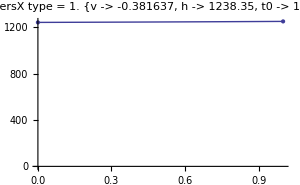
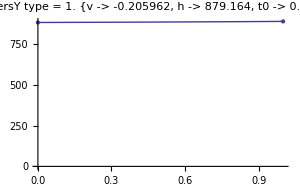

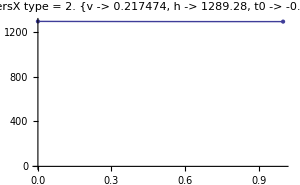
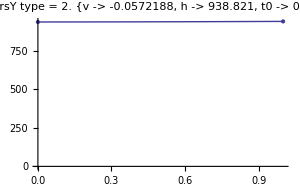

```mathematica
If[showSigmas,
k=1.38*10^(-23);
m=169*1.66*10^(-27);
Clear[t,T,r0,t0];
Radius[t_,T_,r0_,t0_]:=√(r0^2+2*k*T* ((t+t0))^2/m);
shotTipes = Sort[DeleteDuplicates[fitInf[[;;,2]]]];
For[n=1,n≤Length[shotTipes],n++,
listfit=(Select[fitInf,#[[2]]==shotTipes[[n]]&])[[;;,{1,3}]];
resx={#[[1]],4.65*4*σx/.#[[2]]}&/@listfit;
resy={#[[1]],4.65*4*σy/.#[[2]]}&/@listfit;
(*resx=Drop[resx,-1];*)
(*resy=Drop[resy,-1];*)
Quiet[finalFitx=FindFit[resx,Radius[t,T,r0,t0],{T,r0,t0},t];
finalFity=FindFit[resy,Radius[t,T,r0,t0],{T,r0,t0},t];];
Print[Show[ListPlot[resx,PlotLabel->"Temperature X type = "<>ToString[shotTipes[[n]]]<>"\n"<>ToString[finalFitx],AxesOrigin->{0,0}],Plot[Radius[t,T/.finalFitx,r0/.finalFitx,t0/.finalFitx],{t,0,Max[resx[[;;,1]]]}],ImageSize->300],
      Show[ListPlot[resy,PlotLabel->"Temperature Y type = "<>ToString[shotTipes[[n]]]<>"\n"<>ToString[finalFity],AxesOrigin->{0,0}],Plot[Radius[t,T/.finalFity,r0/.finalFity,t0/.finalFity],{t,0,Max[resy[[;;,1]]]}],ImageSize->300]];
];
];
If[showCenters,
shotTipes = Sort[DeleteDuplicates[fitInf[[;;,2]]]];
For[n=1,n≤Length[shotTipes],n++,
listfit=(Select[fitInf,#[[2]]==shotTipes[[n]]&])[[;;,{1,3}]];
centersX={#[[1]],4.65*4*x0/.#[[2]]}&/@listfit;
centersY={#[[1]],4.65*4*y0/.#[[2]]}&/@listfit;
g=9.8 ;
fallFunc[t_,v_,h_,t0_]:=h-v*(t+t0)+g*((t+t0)/2)^2;
fitCentersX= FindFit[centersX,fallFunc[t,v,h,t0],{{v,0},{h,centersX[[1,2]]},{t0,0}},t];
fitCentersY= FindFit[centersY,fallFunc[t,v,h,t0],{{v,0},{h,centersY[[1,2]]},{t0,0}},t];
Print[
Show[
ListPlot[centersX,PlotLabel->"centersX type = "<>ToString[shotTipes[[n]]]<>"\n"<>ToString[fitCentersX],AxesOrigin->{0,0}],Plot[fallFunc[t, v/.fitCentersX,h/.fitCentersX,t0/.fitCentersX],{t,Min[listfit[[;;,1]]],Max[listfit[[;;,1]]]}],ImageSize->300],
       Show[
ListPlot[centersY,PlotLabel->"centersY type = "<>ToString[shotTipes[[n]]]<>"\n"<>ToString[fitCentersY],AxesOrigin->{0,0}],Plot[fallFunc[t, v/.fitCentersY,h/.fitCentersY,t0/.fitCentersY],{t,Min[listfit[[;;,1]]],Max[listfit[[;;,1]]]}],ImageSize->300]];
];
];
```

{{0.,1.,823128.},{0.,2.,891490.},{1.,1.,794338.},{1.,2.,711439.}}

Fit model: a-b ⅇ^(t/τ)

FindFit::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the norm of the residual. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→3.09486×10^10,b→3.09478×10^10,t0→51.,τ→8.28057×10^10}

{a→5.27649,b→5.27649,t0→51.,τ→9.74327×10^6}

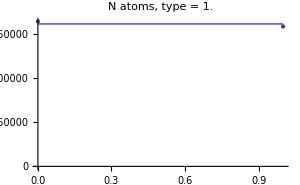
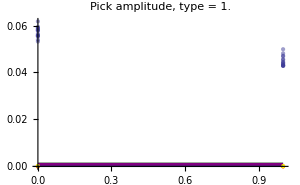
-Graphics-----Graphics-

FindFit::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the norm of the residual. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→1.97789×10^10,b→1.97781×10^10,t0→51.,τ→5.04053×10^10}

{a→163.078,b→163.078,t0→51.,τ→9.71765×10^6}

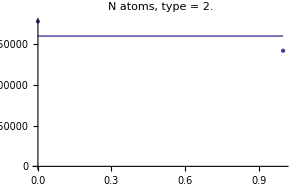
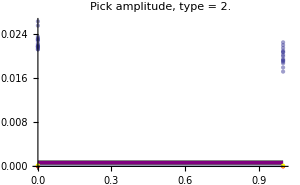
-Graphics-----Graphics-

```mathematica
If[showNatoms,
Clear[power];
power[signal_,gain_,exposure_]:=9.69*10^-3/100*signal/exposure/Exp[3.85/1000*gain];
gamma=10;
angle=1/225;
Isat=180*10^-3;
Int[P_,w_]:=2P/Pi/w^2;
s[P_,w_]:=Int[P,w]/Isat;
ρ[P_,w_,delta_]:=s[P,w]/2/(1+(2*delta/gamma)^2+s[P,w]);
hw=6.6*3/0.41 10^-11;
Nat[delta_,P_,w_,signal_,gain_,exposure_]:=power[signal,gain,exposure]/gamma/hw/ρ[P,w,delta]/angle;
res =Table[
{fitInf[[i,1]],
fitInf[[i,2]],
 Evaluate[Nat[0,2.7,2.27,Abs[a/.fitInf[[i,3]]],100,100]]},
{i,1,Length[fitInf]}];
Print[res];
Clear[a,b,t,t0,τ,modelf];
model = Which[whichModel==1,
a - b*Exp[(t+0*t0)/τ] ,
whichModel==2,
a+b τ^2/((t-t0)^2+(τ)^2)];
Print["Fit model: ",model];
time =Sort [DeleteDuplicates[allInf[[;;,1]]]];
shotTipes = Sort[DeleteDuplicates[res[[;;,2]]]];
For[n=1,n≤Length[shotTipes],n++,
listfit=(Select[res,#[[2]]==shotTipes[[n]]&])[[;;,{1,3}]];
listavr = (Select[avrInf,#[[2]]==shotTipes[[n]]&])[[;;,{1,4}]];
listall = (Select[allInf,#[[3]]==shotTipes[[n]]&])[[;;,{1,5}]];
listfiltered ={#[[1]],Abs[Min[GaussianFilter[#[[3]],filterN]]] }&/@(Select[avrInf,#[[2]]==shotTipes[[n]]&]);
Clear[a,b,t,t0,τ,modelf];
expFit=FindFit[
listfit,
model,
{{a,Which[whichModel==1,60000,whichModel==2,listfit[[1,2]]]},
{b,Which[whichModel==1,60000,whichModel==2,-(100000)]},
{t0,Which[whichModel==1,51,whichModel==2,0]},
{τ,Which[whichModel==1,100,whichModel==2,.300]}},
t];
fitL=FindFit[listavr,
model,
{{a,Which[whichModel==1,60000,whichModel==2,listavr[[1,2]]]},
{b,60000},
{t0,Which[whichModel==1,51,whichModel==2,0]},
{τ,Which[whichModel==1,100,whichModel==2,.400]}},
t];
modelf=Function[{t},Evaluate[model/.fitL]];
Print[expFit];
Print[fitL];
Print[
Show[
ListPlot[listfit,
PlotLabel->"N atoms, type = "<>ToString[shotTipes[[n]]]<>"\n",
PlotStyle->Directive[PointSize[Large]],
AxesOrigin->{0,0},
ImageSize->300],
Plot[(model)/.expFit,{t,Min[time],Max[time]}]],
"---",
Show[
ListPlot[listall,
PlotLabel->"Pick amplitude, type = "<>ToString[shotTipes[[n]]]<>"\n",
PlotStyle->Directive[Opacity[0.5],PointSize[Medium]],
AxesOrigin->{0,0},
ImageSize->300],
ListPlot[listavr,
PlotStyle->Directive[Red,PointSize[Large]]],
ListPlot[listfiltered,
PlotStyle->Directive[Yellow,PointSize[Large]]],
Plot[(model)/.fitL,{t,Min[time],Max[time]}],
Plot[Abs[background],{t,Min[time],Max[time]},PlotStyle->Directive[Green,Thickness[0.01]]],Plot[Abs[noiseLevel],{t,Min[time],Max[time]},PlotStyle->Directive[Purple,Thickness[0.01]]]]]
];
]
```